## Field Plotting

```mathematica
SetDirectory[NotebookDirectory[]];
density32=Import["data/density32.mx"];
```

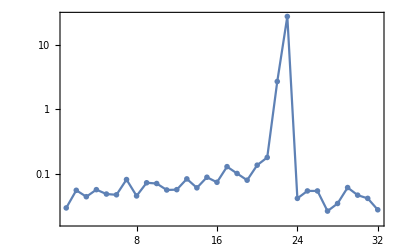

```mathematica
ListLogPlot[Mean@Transpose@density32[[-2]],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,GridLines->Automatic]
```